```mathematica
mainAssoc = stubbornForm2;
```

```mathematica
PartitionToSymbol2[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["p"<>end]]
```

```mathematica
GenerateAxioms2[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[
{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
mainAssoc[key,"colofour"]
]==PartitionToSymbol2[part],
{part,allPartitions}],part]
]
```

```mathematica
baseGraphAxioma2Vars//Length
```

2

```mathematica
baseGraphAxioma2Vars // Length
```

2

```mathematica
prob=GenerateAxioms2[stubbornForm2, 2];
```

```mathematica
newVars=Select[Flatten[Map[ListofVars[#]&,prob]]//Sort,StringStartsQ[SymbolName[#],"p"]&]
```

{p12,p1x2}

```mathematica
Length[newVars]
```

2

```mathematica
sol=First[Solve[prob,baseGraphAxioma2Vars]];
```

```mathematica
GetCoeff[poly_]:=CoefficientList[poly,newVars]
```

```mathematica
Map[#[[2]]&,sol]
```

{-p12+p1x2,p12}

```mathematica
mat2=CoefficientArrays[Map[#[[2]]&,sol],newVars][[2]]
```

SparseArray[<3>, {2, 2}]

```mathematica
MatrixForm[mat2]
```

(-1 | 1
1 | 0)

```mathematica
MatrixForm[Inverse[mat2]]
```

(0 | 1
1 | 1)

```mathematica
Map[Total[#]&,Inverse[mat2]]//Tally//Sort
```

{{1,1},{2,1}}

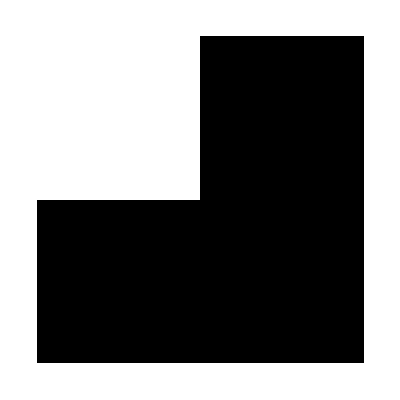

```mathematica
ArrayPlot[Inverse[mat2]]
```

```mathematica
Det[mat2]
```

-1

```mathematica
CharacteristicPolynomial[mat2,x]//Simplify//Factor
```

-1+x+x^2

```mathematica
Tr[mat2]
```

-1

```mathematica
Tr[Inverse[mat2]]
```

1